## Mathematica 8.0 Code for SNNs in the Alexiewicz Topology: A new Perspective to Analysis and Error Bounds Bernhard A. Moser, Inst. of Signal Processing, JKU

1. Functions for Spike Train Generation, LIF Models with different reset modes, Alex-norm

```mathematica
(* general                                                                                   *)
q[a_]:=IntegerPart[Rationalize /@ a]; (* value *)
ceil[a_]:=Ceiling[Rationalize /@ a]; (* value *)
Bernoulli[p_]:= If[RandomReal[]<p, 1, 0];

(* 
represenation of spike train:  eta = (a_i, t_i)_i with spike s = (a, t)                                       *)
keepTime[a_]:= {0,a[[2]]};
weightSpike[a_, w_]:={w*a[[1]], a[[2]]}; 
Lag[a_, Dt_]:= {a[[1]],a[[2]]+Dt};
etaLag[eta_, Dt_]:= Lag[#, Dt]& /@ eta;
causSignal[t_, t0_, a_,alpha_]:= If[t≥ t0, Exp[-alpha*(t-t0)]*a, 0];
feta[t_, eta_, alpha_]:=Sum[causSignal[t, eta[[k,2]], eta[[k,1]],alpha ],{k,1,Length[eta]} ];

(* graphics                                                                                    *)
setY0[a_]:={a[[1]],0};
showSpike[a_]:={setY0[Reverse[a]],Reverse[a]};

(* add two spike trains                                                                                        *)
AddWeightedSpikeTrains[w1_, eta1_,w2_, eta2_]:= Module[{etaNew, eta},
eta = Join[weightSpike[#,w1]& /@ eta1, weightSpike[#,w2]& /@ eta2];
eta = Sort[eta, #1[[2]]≤  #2[[2]]&];
etaNew = {};
While[Length[eta]≥2,
If[eta[[1,2]]==eta[[2,2]], 
etaNew = Append[etaNew, {eta[[1,1]] + eta[[2,1]], eta[[1, 2]]}];
eta  = Drop[eta,2],
etaNew = Append[etaNew, eta[[1]]];
eta  = Drop[eta,1];
];
];
If[Length[eta]==1, etaNew = Append[etaNew, eta[[1]]]];
etaNew
]

(* Alex norm                                                                                                *)
AalphaNorm[eta_,alpha_]:= Max[Table[Abs[Sum[Exp[-alpha*(eta[[k,2]]-eta[[i,2]])]*eta[[i,1]],{i,1,k}]],{k,1,Length[eta]}]];

L2alphaNorm[eta_,alpha_]:=
(Sum[(Sum[Exp[-alpha*(eta[[k,2]]-eta[[i,2]])]*eta[[i,1]],{i,1,k}])^2,
{k,1,Length[eta]}])^(1/2);

(* membrane's potential at end of eta                                                                         *)
Conv[eta_, alpha_]:= Module[{a},
a=Sum[
Exp[
-alpha*(eta[[Length[eta],2]]- eta[[i,2]])
]
*eta[[i,1]],
{i,1,Length[eta]}
];
a //N
]; 

(* generate DN-1 sequence                                                                                     *)
GetNu[Nr_, ExpPar_]:= Module[{a, nu, time},
time = RandomVariate[ExponentialDistribution[ExpPar],Nr];
time = Accumulate[time]; (* increasing sequence *)
a = Table[RandomInteger[{0,1}],{k,1,Nr+1}];
nu = Table[{a[[k+1]]-a[[k]], time[[k]]},{k,1,Nr}]
]

GetEta[Nr_, ExpPar_, pBernoulli_, amplitude_, discreteSteps_]:= Module[{a, nu, time},
(* time = RandomVariate[ExponentialDistribution[ExpPar],Nr];*)
time = Table[RandomReal[{0.2,1}], {k, 1, Nr}];
time = Accumulate[time]; (* increasing sequence *)
a = Table[RandomInteger[{0,1}],{k,1,Nr+1}];
nu = Table[{RandomInteger[{-amplitude,amplitude}]/discreteSteps*Bernoulli[p], time[[k]]},{k,1,Nr}]
]

(* LIF Models                                                                          *)

LeakyIntFireMod[eta_, alpha_, th_]:= Module[{out,pot,potFunction, checkInterval,a},
pot = 0;
out = keepTime[#]& /@ eta;
potFunction = eta;
a = 1;
For[i=1, i ≤ Length[potFunction], i++,
checkInterval = Take[potFunction, {a, i}];
pot = Conv[checkInterval, alpha];
If[Abs[pot]≥ th,  out[[i,1]]= q[pot/th]*th; potFunction[[i,1]] = pot- q[pot/th]*th; a=i;];
];
out
]

LeakyIntFireSub[eta_, alpha_, th_]:= Module[{out,pot,potFunction, checkInterval,a},
pot = 0;
out = keepTime[#]& /@ eta;
potFunction = eta;
a = 1;
For[i=1, i ≤ Length[potFunction], i++,
checkInterval = Take[potFunction, {a, i}];
pot = Conv[checkInterval, alpha];
If[Abs[pot]≥ th,  out[[i,1]]= If[pot>0, th, -th]; potFunction[[i,1]] = pot- If[pot>0, th, -th]; a=i;];
];
out
]

LeakyIntFireZero[eta_, alpha_, th_]:= Module[{out,pot,potFunction, checkInterval,a},
pot = 0;
out = keepTime[#]& /@ eta;
potFunction = eta;
a = 1;
For[i=1, i ≤ Length[potFunction], i++,
checkInterval = Take[potFunction, {a, i}];
pot = Conv[checkInterval, alpha];
If[Abs[pot]≥ th,  out[[i,1]]= If[pot>0, th, -th]; potFunction[[i,1]] =0; a=i;];
];
out
]

(* threshgold error                                                                                                 *)
ThrMod[eta_, Dth_, alpha_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireMod[eta, alpha, th+ Dth] , -1,
 LeakyIntFireMod[eta, alpha, th]], alpha];
ThrSub[eta_, Dth_, alpha_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireSub[eta, alpha, th+ Dth] , -1, 
LeakyIntFireSub[eta, alpha, th]], alpha];
ThrZero[eta_,Dth_, alpha_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireZero[eta, alpha, th+ Dth] ,-1,
LeakyIntFireZero[eta, alpha, th]], alpha];
```

```mathematica
amplitude=4; discreteSteps=4;
eta1 = GetEta[15, 2, 1, amplitude, discreteSteps];
eta2 = GetEta[15, 2, 1,amplitude, discreteSteps];
alpha = 3; (* for membrane *)
```

1.1 Simuation: Membrane’s potential

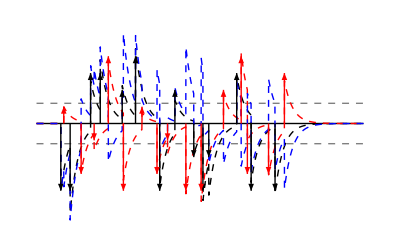

```mathematica
(* spike example                                                                                        *)

plotRange = 13;
pl1 =Plot[{0.3,0,-0.3, 1.5, -1.5},{t, -0.1,plotRange}, PlotRange->All, PlotStyle->{{Dashed,Gray},{Black}, {Dashed,Gray}, {White}, {White}} , Axes->False,
Epilog->Join[Join[{Thick, Arrowheads[.02], Black},Table[Arrow[showSpike[eta1[[k]]]],{k,1,Length[eta1]}]], Join[{Thick,Arrowheads[.02], Red},Table[Arrow[showSpike[eta2[[k]]]],{k,1,Length[eta2]}]]]];
(* membrabe                                                                                                      *)
pl2=Plot[{feta[t, eta1, alpha], feta[t, eta2, alpha],feta[t,AddWeightedSpikeTrains[1,eta1, -1,eta2],alpha]},{t, -0.1,plotRange}, PlotStyle->{{Dashed,Black},{Dashed, Red}, {Dashed, Blue}},PlotRange->All] ;
Show[{pl1, pl2}]
```

2.1 Experiment: Quantization LIF, A norm

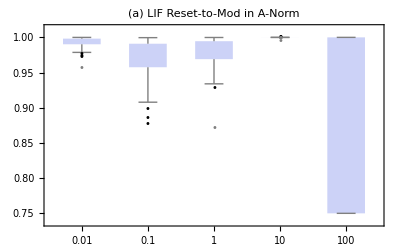
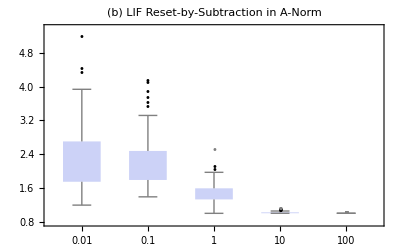
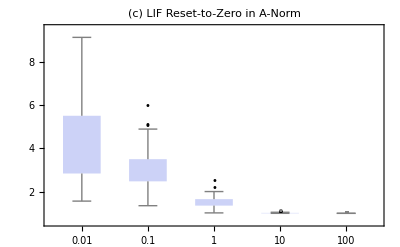
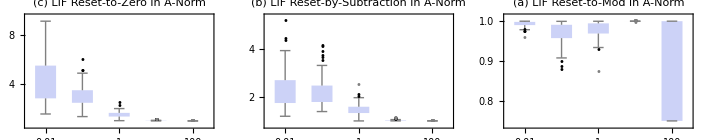
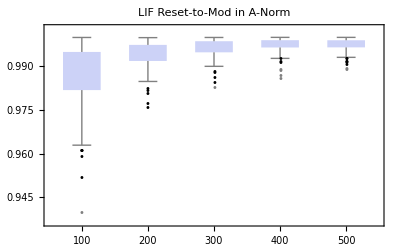
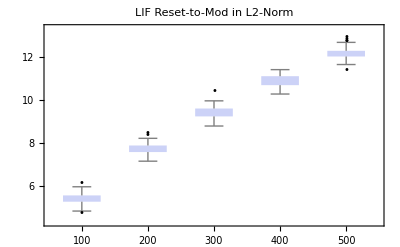
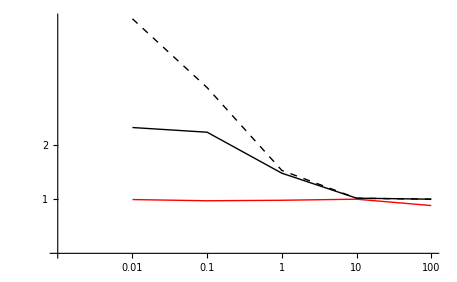
```mathematica
(* Quantization LIF, A norm*)
K = 100;
M = 5;
Nr = 50;
th = 1;
outLeakyModList = Table[Table[0, {k,1, K}], {i,1,M}];
outLeakySubList = Table[Table[0, {k,1, K}], {i,1,M}];
outLeakyZeroList = Table[Table[0, {k,1, K}], {i,1,M}];
alpha = 0.001;
For[n=1, n≤M, n++,
alpha = alpha*10;
For[k = 1,k<=K, k++, 
eta = GetEta[Nr, 1, 1,amplitude, discreteSteps];
outLeakyMod = LeakyIntFireMod[eta, alpha, th];
outLeakySub = LeakyIntFireSub[eta, alpha, th];
outLeakyZero = LeakyIntFireZero[eta, alpha,th];
outLeakyModList[[n,k]] = AalphaNorm[AddWeightedSpikeTrains[1,eta,-1,outLeakyMod],alpha];
outLeakySubList[[n,k]]= AalphaNorm[AddWeightedSpikeTrains[1,eta,-1,outLeakySub],alpha];
outLeakyZeroList[[n,k]]= AalphaNorm[AddWeightedSpikeTrains[1,eta,-1,outLeakyZero],alpha];
];
]

(* Quantization LIF, A-norm*)
data=outLeakyModList;
LIFModPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"0.01","0.1","1", "10", "100"}, PlotLabel->"(a) LIF Reset-to-Mod in A-Norm"]
data=outLeakySubList;
LIFSubPlot = BoxWhiskerChart[data,"Outliers",ChartLabels->{"0.01","0.1","1", "10", "100"}, PlotLabel->"(b) LIF Reset-by-Subtraction in A-Norm"]
data=outLeakyZeroList;
LIFZeroPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"0.01","0.1","1", "10", "100"}, PlotLabel->"(c) LIF Reset-to-Zero in A-Norm"]

GraphicsGrid[{ {LIFZeroPlot,LIFSubPlot,LIFModPlot}}]
-Graphics-
-Graphics-
-Graphics-
-Graphics-

K = 100;
M = 5;
th = 1;
amplitude = 8; 
discreteSteps = 4;
outLeakyListL2 = Table[Table[0, {k,1, K}], {i,1,M}];
outLeakyListA = Table[Table[0, {k,1, K}], {i,1,M}];
alpha = 0.001;
For[n=1, n≤M, n++,
alpha =1;
For[k = 1,k<=K, k++, 
Nr = n*100;
eta =GetEta[Nr, 1, 1,amplitude, discreteSteps];
outLeaky = LeakyIntFireMod[eta, alpha,th];
outLeakyListL2[[n,k]] = L2alphaNorm[AddWeightedSpikeTrains[1,eta,-1,outLeaky],alpha];
outLeakyListA[[n,k]] = AalphaNorm[AddWeightedSpikeTrains[1,eta,-1,outLeaky],alpha];
];
]

data=outLeakyListA;
LIFModPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"100","200","300", "400", "500"}, PlotLabel->"LIF Reset-to-Mod in A-Norm"]

data=outLeakyListL2;
LIFModPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"100","200","300", "400", "500"}, PlotLabel->"LIF Reset-to-Mod in L2-Norm"]

-Graphics-
-Graphics-
ListLinePlot[ {Mean[#] & /@ outLeakyModList,
Mean[#] & /@ outLeakySubList, Mean[#] & /@ outLeakyZeroList}, PlotStyle->{{Red}, {  Blue}, {Black}},
Ticks->{{{1, 0.01},{2,0.1},{3,1},{4,10}, {5,100}},{1,2, 10}}]
-Graphics-
```

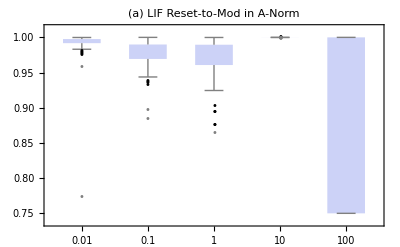

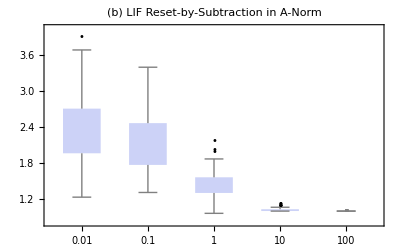

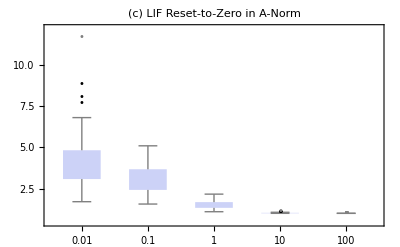

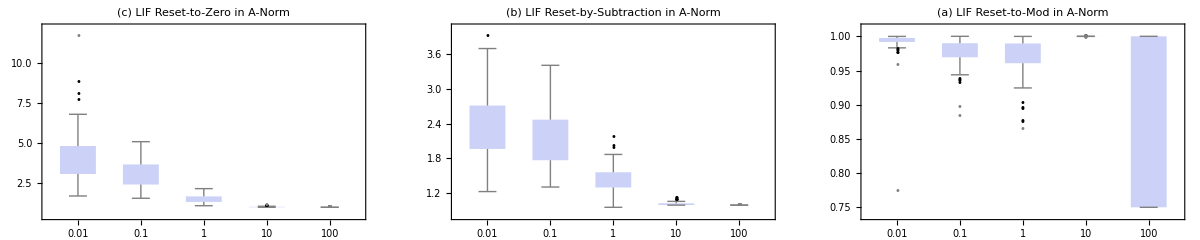

-Graphics-

-Graphics-

-Graphics-

-Graphics-

$Aborted

-Graphics-

-Graphics-

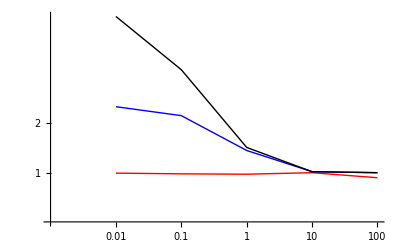

2.2 Experiment: Effect of Threshold Error

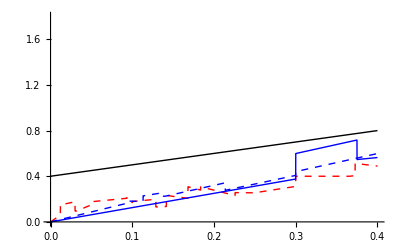

```mathematica
(* show effect of threshold error                                                                      *)

ThrMod[Dth_, alpha_, th_, eta_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireMod[eta, alpha, th+ Dth] , -1, LeakyIntFireMod[eta, alpha, th]], alpha];
ThrSub[Dth_, alpha_, th_,eta_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireSub[eta, alpha, th+ Dth] , -1, LeakyIntFireSub[eta, alpha, th]], alpha];
ThrZero[Dth_, alpha_, th_,eta_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireZero[eta, alpha, th+ Dth] , -1, LeakyIntFireZero[eta, alpha, th]], alpha];

th=0.2; alpha = 0.8;
plotThresholdError =Plot[{0,1.8, 2*th + Dth, 
ThrMod[Dth, alpha,th, eta1],
ThrSub[Dth, alpha,th, eta1],
ThrZero[Dth, alpha,th, eta1]
}, {Dth,0,0.4}, PlotStyle->{{White}, {White},{Thick, Black}, {Dashed,  Red}, { Dashed,Blue}, {Blue}} ]
```

2.3 Experiment: Effect of Time Delay

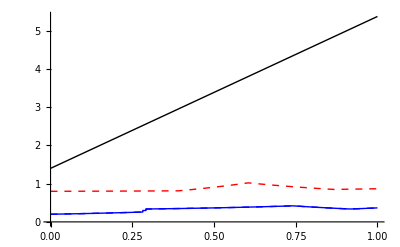

```mathematica
DiffEtaDt[alpha_, eta1_, Dt_]:=AalphaNorm[AddWeightedSpikeTrains[1, eta1, -1, etaLag[eta1, Dt]], alpha];
DiffLIFEtaDtMod[alpha_,eta1_, Dt_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireMod[eta1, alpha, th], -1,  LeakyIntFireMod[etaLag[eta1, Dt], alpha,th]], alpha];
DiffLIFEtaDtSub[alpha_,eta1_, Dt_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireSub[eta1, alpha, th], -1,  LeakyIntFireSub[etaLag[eta1, Dt], alpha,th]], alpha];
DiffLIFEtaDtZero[alpha_,eta1_, Dt_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireZero[eta1, alpha, th], -1,  LeakyIntFireZero[etaLag[eta1, Dt], alpha,th]], alpha];

th=0.2; alpha = 2;
plotDelayError =Plot[{0,2*th + 1 + alpha*Dt* (AalphaNorm[eta1,alpha]+ 1), 
DiffLIFEtaDtMod[alpha,eta1,  Dt, th],
DiffLIFEtaDtSub[alpha,eta1,  Dt, th],
DiffLIFEtaDtZero[alpha,eta1,  Dt, th]
}, {Dt,0,1}, PlotStyle->{{White}, {Thick, Black}, {Dashed,  Red}, { Dashed,Blue}, {Blue}} ]
```

2.4 Experiment: Quasi Isometry

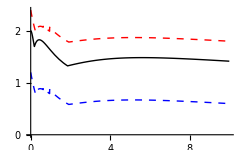

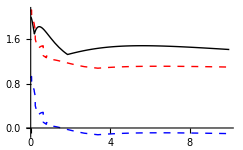

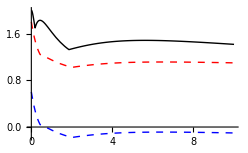

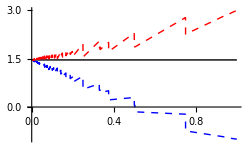

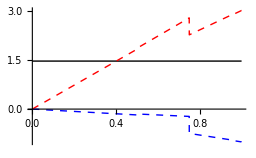

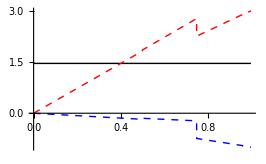

```mathematica
DiffEta[alpha_, eta1_, eta2_]:=AalphaNorm[AddWeightedSpikeTrains[1, eta1, -1, eta2], alpha];
DiffLIFEtaMod[alpha_,eta1_, eta2_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireMod[eta1, alpha, th], -1,  LeakyIntFireMod[eta2, alpha,th]], alpha];
DiffLIFEtaSub[alpha_,eta1_, eta2_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireSub[eta1, alpha, th], -1,  LeakyIntFireSub[eta2, alpha,th]], alpha];
DiffLIFEtaZero[alpha_,eta1_, eta2_, th_]:=AalphaNorm[AddWeightedSpikeTrains[1, LeakyIntFireZero[eta1, alpha, th], -1,  LeakyIntFireZero[eta2, alpha,th]], alpha];


th=0.3;
Plot[{0, DiffEta[alpha, eta1, eta2],DiffLIFEtaMod[alpha,eta1, eta2, th]-2*th, DiffLIFEtaMod[alpha,eta1, eta2, th]+2*th}, {alpha, 0,10}, PlotRange->All, PlotStyle->{{White},{Thick,Black}, {Dashed,Blue}, {Dashed,Red}}]

Plot[{0, DiffEta[alpha, eta1, eta2],DiffLIFEtaSub[alpha,eta1, eta2, th]-2*th, DiffLIFEtaSub[alpha,eta1, eta2, th]+2*th}, {alpha, 0,10}, PlotRange->All, PlotStyle->{{White},{Thick,Black}, {Dashed,Blue}, {Dashed,Red}}]

Plot[{0, DiffEta[alpha, eta1, eta2],DiffLIFEtaZero[alpha,eta1, eta2, th]-2*th, DiffLIFEtaZero[alpha,eta1, eta2, th]+2*th}, {alpha, 0,10}, PlotRange->All, PlotStyle->{{White},{Thick, Black}, {Dashed,Blue}, {Dashed,Red}}]

(* th -> 0, alpha = 1 *)

alpha = 4;
Plot[{0, DiffEta[alpha, eta1, eta2],DiffLIFEtaMod[alpha,eta1, eta2, th]-2*(th), DiffLIFEtaMod[alpha,eta1, eta2, th]+2*(th)}, {th, 0,1}, PlotRange->All, PlotStyle->{{White},{Thick,Black}, {Dashed,Blue}, {Dashed,Red}}]

Plot[{0, DiffEta[alpha, eta1, eta2],DiffLIFEtaSub[alpha,eta1, eta2, th]-2*(th), DiffLIFEtaSub[alpha,eta1, eta2, th]+2*(th)}, {th, 0,1}, PlotRange->All, PlotStyle->{{White},{Thick,Black}, {Dashed,Blue}, {Dashed,Red}}]

Plot[{0, DiffEta[alpha, eta1, eta2],DiffLIFEtaZero[alpha,eta1, eta2, th]-2*(th), DiffLIFEtaZero[alpha,eta1, eta2, th]+2*(th)}, {th, 0,1}, PlotRange->All, PlotStyle->{{White},{Thick, Black}, {Dashed,Blue}, {Dashed,Red}}]
```

2.5 Experiment: Resonance Phenomenon

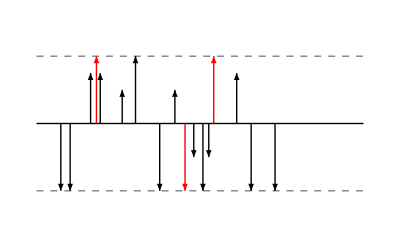

```mathematica
(* Resonance Phenomenon / Lipschitz Sytle Upper Bound                                                 *)
(* noise example                                                                                      *)
nu1p[p_]:= {{1*p, 2.3},{-1*p, 5.85}, {1*p, 7}} ;

resFunZero[eta1_, alpha_,p_, th_]:=Module[{DeltaEta},
DeltaEta = AddWeightedSpikeTrains[1, LeakyIntFireZero[AddWeightedSpikeTrains[1,eta1, 1,nu1p[p]], alpha, th], -1, LeakyIntFireZero[eta1, alpha,th]];
AalphaNorm[DeltaEta, alpha]
];

resFunMod[eta1_,alpha_,p_,th_]:=Module[{DeltaEta},
DeltaEta = AddWeightedSpikeTrains[1, LeakyIntFireMod[AddWeightedSpikeTrains[1,eta1, 1,nu1p[p]], alpha, th], -1, LeakyIntFireMod[eta1, alpha,th]];
AalphaNorm[DeltaEta, alpha]
];

resFunSub[eta1_,alpha_,p_, th_]:=Module[{DeltaEta},
DeltaEta = AddWeightedSpikeTrains[1, LeakyIntFireSub[AddWeightedSpikeTrains[1,eta1, 1,nu1p[p]], alpha, th], -1, LeakyIntFireSub[eta1, alpha, th]];
AalphaNorm[DeltaEta, alpha]
];

(* Graphics                                                                                          *)
pl1 =Plot[{1,0,-1, 1.5, -1.5},{t, -0.1,13}, PlotRange->All, PlotStyle->{{Dashed,Gray},{Black}, {Dashed,Gray}, {White}, {White}} , Axes->False,
Epilog->Join[Join[{Arrowheads[.02], Black},Table[Arrow[showSpike[eta1[[k]]]],{k,1,Length[eta1]}]], Join[{Arrowheads[.02], Red},Table[Arrow[showSpike[nu1p[1][[k]]]],{k,1,Length[nu1p[1]]}]]]]
```

```mathematica
alpha = 0.1; th = 1;

pl2Mod = Plot3D[resFunMod[eta1, alpha, p, th],{alpha,0,10},{p,0,1},MeshStyle->{({Red,Tube@@#}&),Directive[White],Directive[Black]},
MeshFunctions->{#1&, #3&,#2&},Mesh->{{0},20,20},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

```mathematica
pl2Zero = Plot3D[resFunZero[eta1,alpha, p, th],{alpha,0,10},{p,0,1},MeshStyle->{({Red,Tube@@#}&),Directive[White],Directive[Black]},
MeshFunctions->{#1&, #3&,#2&},Mesh->{{0},20,20},ColorFunction->"BlueGreenYellow"]

pl2Sub = Plot3D[resFunSub[eta1,alpha, p, th],{alpha,0,10},{p,0,1},MeshStyle->{({Red,Tube@@#}&),Directive[White],Directive[Black]},
MeshFunctions->{#1&, #3&,#2&},Mesh->{{0},20,20},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Add. Error, LIF, A norm*)
K = 30; (* runs for different nu *)
M = 4; (* alphas *)
Nr= 30; (* spikes *)
amplitude= 8;
discreteSteps = 4;
outLeakyModList = Table[Table[0, {k,1, K}], {i,1,M}];
outLeakySubList = Table[Table[0, {k,1, K}], {i,1,M}];
outLeakyZeroList = Table[Table[0, {k,1, K}], {i,1,M}];
alpha = 0.01;
th = 1;
(* alpha *)
For[n=1, n≤M, n++,
If[n ==1,alpha =0];
If[n ==2,alpha =0.01];
alpha = alpha*10;
(* eta *)
For[k = 1,k<=K, k++, 
eta =  GetEta[Nr, 1, 1,amplitude, discreteSteps];
outLeakyMod = LeakyIntFireMod[eta, alpha,th];
outLeakySub = LeakyIntFireSub[eta, alpha,th];
outLeakyZero = LeakyIntFireZero[eta, alpha,th];

(* nu *)
For[m = 1,m<=K, m++,
nu = GetNu[Nr, 1];
etaPlusNu = AddWeightedSpikeTrains[1, eta, 1, nu];
outLeakyModNu = LeakyIntFireMod[etaPlusNu, alpha, th];
outLeakySubNu = LeakyIntFireSub[etaPlusNu, alpha, th];
outLeakyZeroNu = LeakyIntFireZero[etaPlusNu, alpha,th];

outLeakyModList[[n,k]] = AalphaNorm[AddWeightedSpikeTrains[1, outLeakyModNu,-1,outLeakyMod ], alpha];
outLeakySubList[[n,k]]= AalphaNorm[AddWeightedSpikeTrains[1, outLeakySubNu,-1,outLeakySub ], alpha];
outLeakyZeroList[[n,k]]= AalphaNorm[AddWeightedSpikeTrains[1, outLeakyZeroNu,-1,outLeakyZero ], alpha];
]
];
]
```

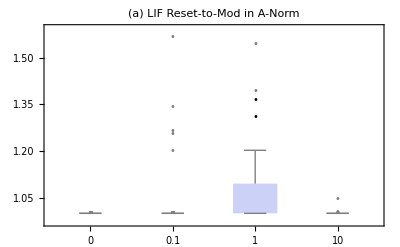

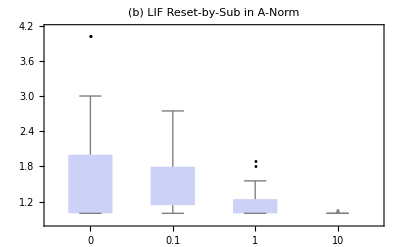

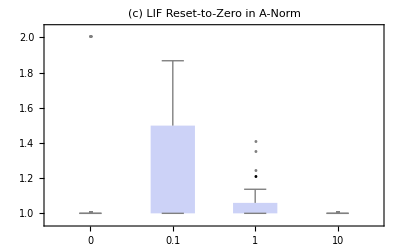

{0.,0,1}

```mathematica
data=outLeakyModList;
LIFModPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"0","0.1","1", "10", "100"}, PlotLabel->"(a) LIF Reset-to-Mod in A-Norm"]
data=outLeakySubList;
LIFModPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"0","0.1","1", "10", "100"}, PlotLabel->"(b) LIF Reset-by-Sub in A-Norm"]
data=outLeakyZeroList;
LIFModPlot= BoxWhiskerChart[data,"Outliers",ChartLabels->{"0","0.1","1", "10", "100"}, PlotLabel->"(c) LIF Reset-to-Zero in A-Norm"]
```

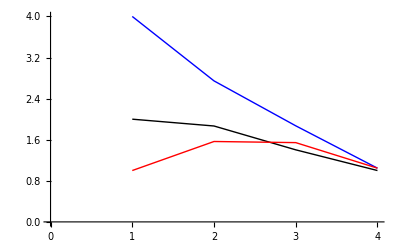

```mathematica
ListLinePlot[{Table[Max[outLeakyZeroList[[n, All]]], {n,1,4}], Table[Max[outLeakySubList[[n, All]]], {n,1,4}], Table[Max[outLeakyModList[[n, All]]], {n,1,4}]}, 
PlotStyle->{Black, Blue, Red}, Ticks->{{{1,0}, {2,0.1}, {3, 1}, {4,10}}}]
```